## SimShow-example.nb SimShow, SimShowAt, SimShowFinal

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51f (14 June 2017)) loaded Wed 14 Jun 2017 16:48:29
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
<<xlr8r.m
```

xCellerator 0.95 (28-Feb-2014) loaded Wed 14 Jun 2017 16:48:42
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

85 cells

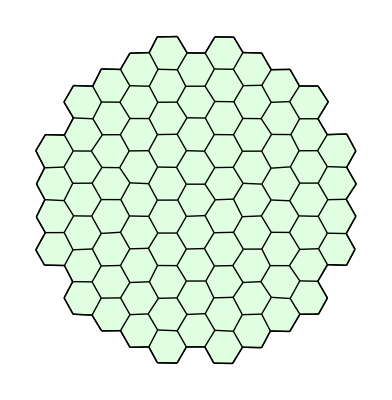

```mathematica
w=TemplateCircularHoneycombCover[7];
Print[NTissueCells[w]," cells"];
w=RandomizeTemplate[w, 0.05];
ShowTissue[w]
```

The following network is a mass-action implementation of the simple harmonic oscillator.

```mathematica
net = {{X+Y-> X, k1/Y[t]}, {Y-> Y+X, k2}};
parameters = {k1-> 1, k2-> 1}; 
interpret[net]/.parameters
```

{{X'[t]==Y[t],Y'[t]==-X[t]},{X,Y}}

Demonstrate that it works as a stand-alone network

```mathematica
s=run[net/.parameters, initialConditions-> {X-> 1, Y-> 1}, timeSpan-> 10];
```

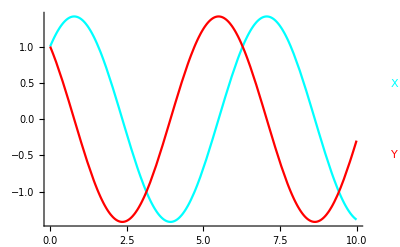

```mathematica
runPlot[s]
```

extend the network to the entire shebang

```mathematica
bignet=CelleratorNetwork[w, "Reactions"-> net, "Diffusion"-> {{X, DX}}];
```

85 Cells.

2 internal reactions in each cell.

170 intracellular reactions.

444 diffusion reactions.

614 total reactions.

generate initial conditions on the template

```mathematica
myic=Table[{X[i]-> RandomReal[{-1,1}], Y[i]-> RandomReal[{-1,1}]}, {i, 1, 100}]//Flatten;
```

run a simulation on the template

```mathematica
sim=RunSim[bignet/.{DX-> .5}, parameters, myic, {0,50}];
```

use SimPlot to plot the value of X in every cell during the entire simulation

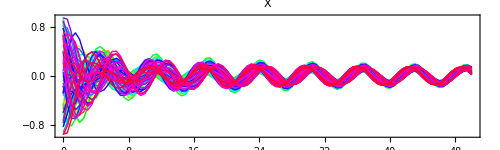

```mathematica
SimPlot[sim,X, AspectRatio-> .3, ImageSize-> 500]
```

Use SimShowFinal to show the concentrations at the end of the simulation with automatic scaling.

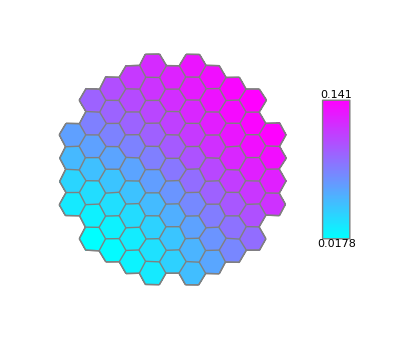

```mathematica
SimShowFinal[sim,X, w, {Cyan, Magenta}, "EdgeStyles"-> Gray]
```

Use SimShow to show a snapshot of the solution at a given time

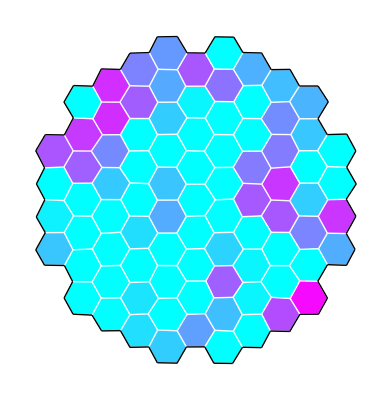

```mathematica
SimShow[sim, X, 0.25, w, {Cyan, Magenta}, {0, 1}, "EdgeStyles"-> White]
```

Use SimShowAt to show a legend

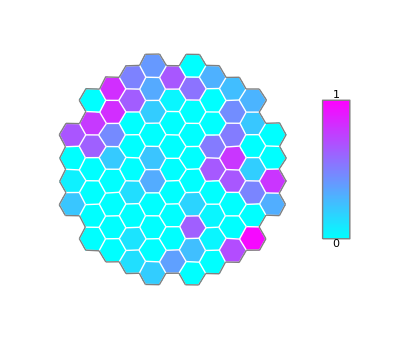

```mathematica
SimShowAt[sim, X, 0.25, w, {Cyan, Magenta}, {0, 1}, "EdgeStyles"-> White]
```

Use SimeShowAt to Show a legend and Autoscale the Range

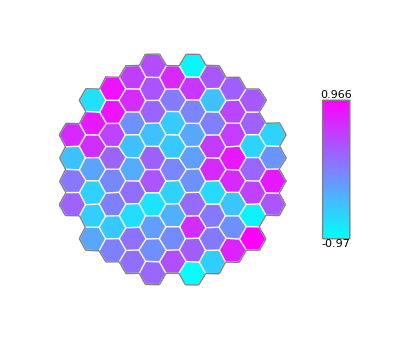

```mathematica
SimShowAt[sim, X, 0.25, w, {Cyan, Magenta}, "EdgeStyles"-> White]
```

save plots for movie generation

```mathematica
plots=Table[SimShowAt[sim, X, t, w, {Cyan, Magenta}, "EdgeStyles"-> White],{t, 0,40,.25}];
```

```mathematica
ListAnimate[plots]
```

```mathematica
SaveFrames[plots,"jpg",300,"mov","hex-sho"];
```

Created folder: /Users/mathman/Cellzilla/Simulations-14-Jun-17/hex-sho14Jun17-1702

movie file will be: hex-sho14Jun17-1702.mov

movie file will be in the folder: /Users/mathman/Cellzilla/Simulations-14-Jun-17/hex-sho14Jun17-1702

Created directory: /Users/mathman/Cellzilla/Simulations-14-Jun-17/hex-sho14Jun17-1702/Frames

Putting movie frames in  in /Users/mathman/Cellzilla/Simulations-14-Jun-17/hex-sho14Jun17-1702/Frames

ffmpeg -r 16 -i 'FRAME%4d.jpg' 'hex-sho14Jun17-1702.mov'

ERROR: Unable to produce movie. ffmpeg return code is: 32512 On some versions of Mathematica (such as the version installed on this computer), the Kernel is unable to locate the correct path execute ffmpeg. You must do this manually:

In a command shell such as bash, terminal, or cmd, change your current working directory to (e.g., with the cd command):
 cd /Users/mathman/Cellzilla/Simulations-14-Jun-17/hex-sho14Jun17-1702
Then type the following:
ffmpeg -r 16 -i 'FRAME%4d.jpg' 'hex-sho14Jun17-1702.mov'
You can change the last field to whatever you want the movie to actually be called. In this case, it will be called hex-sho14Jun17-1702.mov and be in the same folder as all the frames.